```mathematica
Annihilation and g-2 Fit
```

```mathematica
Clear[Ml]
Ml=300;
mu=0.105;
a = 3*^-9;
omega = 2.5*^-12;
Ncm = 1;
Ncq = 3;
```

```mathematica
d[t_]:=(11*t^2-7*t+2)/(18*(t-1)^3) - (t^3*Log[t])/(3*(t-1)^4);
c[t_]:=(3*t-1)/(4*(t-1)^2) - (t^2*Log[t])/(2*(t-1)^3);
p[g_,M_]:= g^2*mu^2/(16*Pi^2) * 1/M^2;
```

```mathematica
da[t_,g_,M_]:=p[g,M]*(3/2*d[t]-c[t]) ;
annDir[t_,g_,M_,Nc_]:=Nc * g^4/(32*Pi*M^2) * t/(t+1)^2;
```

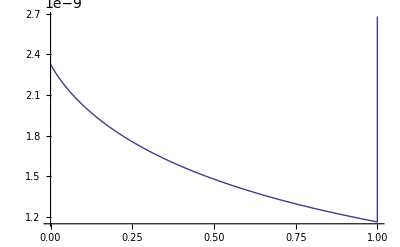

```mathematica
Plot[da[t,6,Ml,Ncm],{t,0,1*^-0}]
```

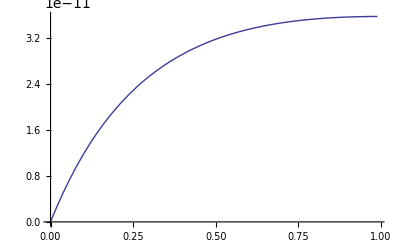

```mathematica
Plot[annDir[t,0.0006,Ml,Ncm],{t,0,0.99}]
```

```mathematica
annDir[1*^-8,6.,300,Ncm]
da[1*^-8,6,300]
```

```mathematica
Solve[annDir[1*^-8,g,M,Ncm] == omega && da[1*^-8,g,M]==a, {g,M}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g→-6.98149,M→-307.451},{g→-6.98149,M→307.451},{g→6.98149,M→-307.451},{g→6.98149,M→307.451}}

## Gripaios g-2

```mathematica
cbar = c;
dbar = d;
c1[t_]:= -c[1/t]/t;
d1[t_]:=d[1/t]/t;
k[t_]:= c[t]+3/2*d[t];
kbar[t_]:= cbar[t]+3/2*dbar[t];
sigmaF[Q_,t_]:=Q*k[t];
sigmaB[Q_,t_]:=Q*kbar[t];
aGrip[t_, M_, qf1_, qf2_, qb1_, qb2_, mu_, g_]:= g^2/(6Pi^ 2
```